Objective:

We want to maximize the net benefits of one farmer subject to population growth.

Setup:

The farmer wants to maximize his net benefits by choosing a level of harvest.

On the revenue side, we have the positive revenue from crop output (Y) and price (p) and the loss in revenue from the damage to the crop (d) made by the hogs after harvest (N-H). It is assumed that damage intensity increases as more hogs are present. This results in the exponential parameter (beta) added to the damage term st d(N-H)^beta. The full revenue term is then p(Y-d(N-H)^beta)

On the cost side, we include a fixed farming cost (s) to include any cost of planting or seeds and a variable farming cost (mu) to include any additional cost caused by an increase in hogs compared to their carrying capacity on the farm (N/theta). This would include things like damage to facilities due to rooting or wallowing. We include a fixed cost of harvest (c0) and a variable cost of harvesting dependent on the proportion harvested. As the population decreases, it becomes harder and more costlier to harvest each hog as they tend to evade harvest. This is represented as ac1H/N where (a) is the avoidance level, c1 is the cost of harvest, H is the harvested hogs, and N is the total population. The full cost term is then s(1+mu(N/theta))+c0+ac1H/N

We have two equations of motion. 
The first is the well loved logistic growth function:
N’=N+rN(1-N/theta)-H

Equation Set up

```mathematica
profit    = p*(Y - d*(Nt - Ht)^beta) - s*(1 + mu*(Nt/theta)) - c0 - (A*c1*Ht)/Nt
popEM      = Nt+r*Nt*(1-Nt/theta)-Ht-Nt1
```

-(A c1 Ht)/Nt+p (Y-d (Nt-Ht)^beta)-c0-s ((mu Nt)/theta+1)

-Ht+Nt r (1-Nt/theta)+Nt-Nt1

We need to set up the Lagrangian equation and take derivatives. We needed to add in a rho*lamt to the pop deriv by hand to make up for the missing Nt1 that did not make it into the derivatives(mathematica naming).

```mathematica
Lagran = rhot*(profit + rho*lamt1*(popEM))
controlderiv = D[Lagran, Ht]
popderiv = D[Lagran, Nt]-rhot*lamt
```

rhot (-(A c1 Ht)/Nt+p (Y-d (Nt-Ht)^beta)-c0+lamt1 rho (-Ht+Nt r (1-Nt/theta)+Nt-Nt1)-s ((mu Nt)/theta+1))

rhot (-(A c1)/Nt+beta d p (Nt-Ht)^(beta-1)-lamt1 rho)

rhot ((A c1 Ht)/Nt^2-beta d p (Nt-Ht)^(beta-1)+lamt1 rho (r (1-Nt/theta)-(Nt r)/theta+1)-(mu s)/theta)-lamt rhot

Solving Lagrange Multipliers

Under steady state conditions, t+1=t or t1=t.

```mathematica
controlderivSS = controlderiv/.{Nt->Ns,Ht->Hs,lamt1->lam,lamt->lam,rhot->1}
popderivSS =popderiv/. {Nt->Ns,Ht->Hs,lamt1->lam,lamt->lam,rhot->1}
popEMSS1     = popEM/.{Nt->Ns,Ht->Hs,Nt1->Ns}
```

-(A c1)/Ns+beta d p (Ns-Hs)^(beta-1)-lam rho

(A c1 Hs)/Ns^2-beta d p (Ns-Hs)^(beta-1)+lam rho (r (1-Ns/theta)-(Ns r)/theta+1)-lam-(mu s)/theta

Ns r (1-Ns/theta)-Hs

We need to solve for delta

```mathematica
(* Solve for lambdarh from the controlderivSS equation*)
lamrho=-(A c1)/Ns+beta d p (Ns-Hs)^(beta-1);
(* Rewriting lamrho equation so it includes delta such that rho=1/1+delta and solves for lam*)
lam1=(-(A c1)/Ns+beta d p (Ns-Hs)^(beta-1))*(1+delta);
(* Solve for lam from popsderivss and plugging in the value from the lamrho equation *)
lam2=(A c1 Hs)/Ns^2-beta d p (Ns-Hs)^(beta-1)+lamrho (r (1-Ns/theta)-(Ns r)/theta+1)-(mu s)/theta;
(* Setting the two lam equations , lam1 and lam2 equal and solveing for delta. then putting everything on one side such that when equal to zero, we get our SS*)

FTRR=((A c1 Hs)/Ns^2-beta d p (Ns-Hs)^(beta-1)+lamrho (r (1-Ns/theta)-(Ns r)/theta+1)-(mu s)/theta)/(-(A c1)/Ns+beta d p (Ns-Hs)^(beta-1))-1-delta
(* plugging in Hs value so it is only in terms of Ns*)
beta=2
FRR=FTRR/.{Hs->Ns*r*(1-Ns/theta)}
```

((r (1-Ns/theta)-(Ns r)/theta+1) (beta d p (Ns-Hs)^(beta-1)-(A c1)/Ns)+(A c1 Hs)/Ns^2-beta d p (Ns-Hs)^(beta-1)-(mu s)/theta)/(beta d p (Ns-Hs)^(beta-1)-(A c1)/Ns)-delta-1

2

((r (1-Ns/theta)-(Ns r)/theta+1) (2 d p (Ns-Ns r (1-Ns/theta))-(A c1)/Ns)+(A c1 r (1-Ns/theta))/Ns-2 d p (Ns-Ns r (1-Ns/theta))-(mu s)/theta)/(2 d p (Ns-Ns r (1-Ns/theta))-(A c1)/Ns)-delta-1

```mathematica
(* Setting rho equal to 1 so we can look at SS paths and phase diagrams*)
controlderivSS = controlderiv/.{rhot->1};
popderivSS =popderiv/. {rhot->1};
popEMSS     = popEM
(* Need to solve for lambda again *)
lamtt1=(-(A c1)/Ns+beta d p (Nt-Ht)^(beta-1))*(1+delta);
lamt1rho=-(A c1)/Nt+beta d p (Nt-Ht)^(beta-1);
lamtt2=(A c1 Ht1)/Nt1^2-beta d p (Nt1-Ht1)^(beta-1)+lamt1rho (r (1-Nt1/theta)-(Nt1 r)/theta+1)-(mu s)/theta;
```

-Ht+0.584 (1-Nt/50) Nt+Nt-Nt1

```mathematica
beta=2;
(*plug lambdas into controlderivSS equation*)
harvsol=(-(A c1)/Ns+beta d p (Nt-Ht)^(beta-1))*(1+delta)-(A c1 Ht1)/Nt1^2+beta d p (Nt1-Ht1)^(beta-1)-((r (1-Nt1/theta)-(Nt1 r)/theta+1) *(beta d p (Nt-Ht)^(beta-1)-(A c1)/Nt))+(mu s)/theta
(*solve for ht+1*)
Hsol=Ht1/.Solve[{harvsol==0},Ht1]
(*plug in the value for Nt+1 (Nt1)*)
Hsol1=Hsol/.{Nt1->Ns* r (1-Ns/theta)+Ns-Hs,Nt->Ns,Ht->Hs} (*Ht+1 equation*)
Psol1=Ns+r*Ns*(1-Ns/theta)-Hs (*Nt+1 equation*)
```

1.1 (0.04 (Nt-Ht)-20/Ns)-(0.584 (1-Nt1/50)-0.01168 Nt1+1) (0.04 (Nt-Ht)-20/Nt)-(20 Ht1)/Nt1^2+0.04 (Nt1-Ht1)+0.6

{(1. (0.584 (1.-0.02 Nt1)-0.01168 Nt1+1.) (0.04 (Nt-1. Ht)-20./Nt)-1.1 (0.04 (Nt-1. Ht)-20./Ns)-0.04 Nt1-0.6)/(-20./Nt1^2-0.04)}

{(1. (0.04 (Ns-1. Hs)-20./Ns) (0.584 (1.-0.02 (-Hs+0.584 (1-Ns/50) Ns+Ns))-0.01168 (-Hs+0.584 (1-Ns/50) Ns+Ns)+1.)-0.04 (-Hs+0.584 (1-Ns/50) Ns+Ns)-1.1 (0.04 (Ns-1. Hs)-20./Ns)-0.6)/(-20./(-Hs+0.584 (1-Ns/50) Ns+Ns)^2-0.04)}

-Hs+0.584 (1-Ns/50) Ns+Ns

```mathematica
(*seting up equations to solve for steady state*)
c1=130;
c0=100;
theta=50;
p=0.1;
r=0.584;
s=600;
delta=0.1;
d=0.5;
mu=0.1;
A=1;
```

```mathematica
(* plug Ht+1 and Nt+1 equation into this new format*)
g[Hs_,Ns_]:=1/(Ns^2 theta (-A c1-2 d p (-Hs+Ns r (1-Ns/theta)+Ns)^2))(-Hs+Ns r (1-Ns/theta)+Ns)^2 (A c1 delta Ns theta+2 A c1 Ns r (-Hs+Ns r (1-Ns/theta)+Ns)-A c1 Ns r theta+2 d delta Hs Ns^2 p theta-2 d delta Ns^3 p theta-4 d Ns^3 p r (-Hs+Ns r (1-Ns/theta)+Ns)+4 d Hs Ns^2 p r (-Hs+Ns r (1-Ns/theta)+Ns)-2 d Hs Ns^2 p r theta-2 d Ns^2 p theta (-Hs+Ns r (1-Ns/theta)+Ns)+2 d Ns^3 p r theta-mu Ns^2 s)
f[Hs_,Ns_]:=Ns+r*Ns(1-Ns/theta)-Hs
(*check equations*)
g[Hs,Ns]
f[Hs,Ns]
```

((-Hs+0.584 (1-Ns/50) Ns+Ns)^2 (-0.1168 Ns^3 (-Hs+0.584 (1-Ns/50) Ns+Ns)-2.42 Hs Ns^2+0.1168 Hs Ns^2 (-Hs+0.584 (1-Ns/50) Ns+Ns)-5. Ns^2 (-Hs+0.584 (1-Ns/50) Ns+Ns)+151.84 Ns (-Hs+0.584 (1-Ns/50) Ns+Ns)+2.42 Ns^3-60. Ns^2-3146. Ns))/(50 Ns^2 (-0.1 (-Hs+0.584 (1-Ns/50) Ns+Ns)^2-130))

-Hs+0.584 (1-Ns/50) Ns+Ns

```mathematica
(*Solve for steady state: setting Ht+1 = Ht and Nt+1 = Nt and solving for Ns and Hs*)
Simplify[Solve[{Hs==g[Hs,Ns],Ns==f[Hs,Ns]},{Hs,Ns}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Hs→-58.0197,Ns→-49.7826},{Hs→-0.728254-18.7003 ⅈ,Ns→-9.85477-22.9675 ⅈ},{Hs→-0.728254+18.7003 ⅈ,Ns→-9.85477+22.9675 ⅈ},{Hs→5.26076,Ns→11.7867}}

```mathematica
{{Hs->-63.51932640920479,Ns->-52.86718496220835},{Hs->2.657744075903931-17.946068376150023 ⅈ,Ns->-6.500046044965078-24.38851128453744 ⅈ},{Hs->2.657744075903931+17.946068376150023 ⅈ,Ns->-6.500046044965078+24.38851128453744 ⅈ},{Hs->3.9884272984928146,Ns->8.16179760008371}}
```

{{Hs→-63.5193,Ns→-52.8672},{Hs→2.65774-17.9461 ⅈ,Ns→-6.50005-24.3885 ⅈ},{Hs→2.65774+17.9461 ⅈ,Ns→-6.50005+24.3885 ⅈ},{Hs→3.98843,Ns→8.1618}}

```mathematica
(* Solving for Isoclines. SOlve both equations for y*)
Harviso=Hs/.Solve[g[Hs,Ns]-Hs==0,Hs][[1]]
Popiso=Hs/.Solve[f[Hs,Ns]-Ns==0,Hs][[1]]
```

```mathematica
(* Using the equations to solve for Hs, we set them equal to each other and solve for Ns*)
P1=Ns/.Simplify[Solve[Harviso==Popiso,Ns]][[1]]
```

```mathematica
(* Plug the Ns value back into the Harviso equation*)
H1=Harviso/.Ns->P1
```

```mathematica
(* Plot the isocline*)
Plot[{Harviso,Popiso},{Ns,0.1,20},PlotRange->{{0,20},{-100,10}}]
```

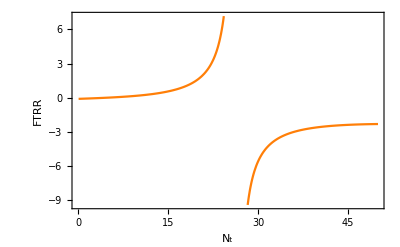

```mathematica
(* plotting fund theorem across population*)
Plot[FRR==0,{Ns,0.1,50},Frame->True,FrameLabel->{"N_t","FTRR"}]
```

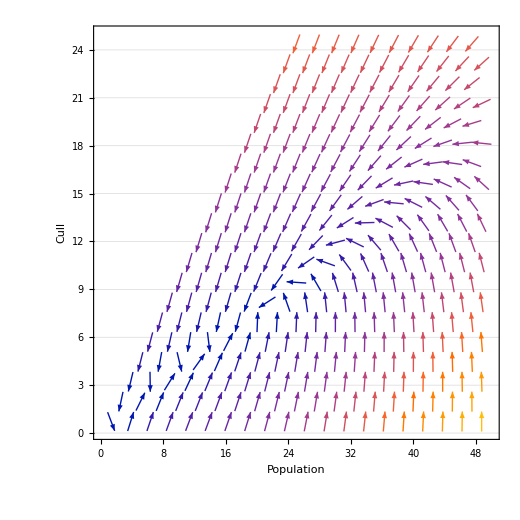

```mathematica
Plot1=VectorPlot[{f[Hs,Ns]-Ns,g[Hs,Ns]-Hs},{Ns,0.1,50},{Hs,0.1,25},(*Control of LINE OR POINT APPEARANCE*)VectorPoints->{20,20},VectorScale->{0.05,0.5},VectorStyle->{Gray},(*Restrict the vectors to the region where Ns>Hs*)RegionFunction->(#2<=#1&),RegionBoundaryStyle->None,RegionFillingStyle->None,(*#1 corresponds to Hs,and #2 to Ns*)(*Controls of Frame and AXES*)AxesOrigin->{-1,0},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->True,BaseStyle->{24,FontFamily->"Times"},GridLines->{None,Automatic},GridLinesStyle->Directive[Dashed],(*Controls of LABELS*)AspectRatio->1,ImageSize->520]
```

Part::partd: Part specification 50.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 25.⟦1⟧ is longer than depth of object.

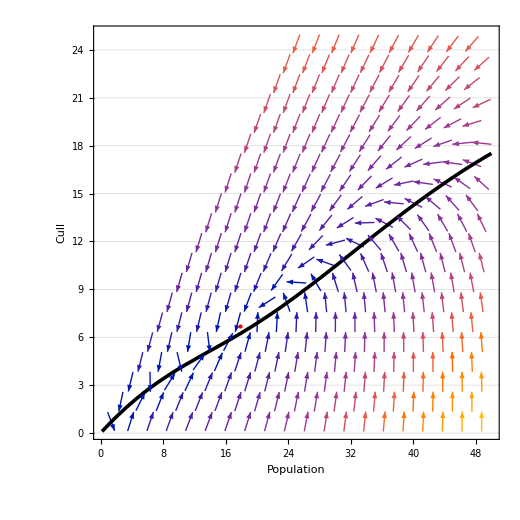

```mathematica
c1=130;
c0=100;
theta=50;
p=0.1;
r=0.584;
s=600;
delta=0.1;
d=0.35;
mu=0.1;
A=1;
(*Plot only the rightmost contour line*)
Plot2=ContourPlot[g[Hs,Ns]-Hs==0,{Ns,0.1,50},{Hs,0.1,25},ContourStyle->{Black,Thickness[0.005]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->False,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];

(*Extract the contour data*)
contours=Cases[Normal[Plot2],Line[pts_]:>pts,Infinity];

(*Sort the contours by the maximum x-coordinate value*)
sortedContours=SortBy[contours,Max[#][[1]]&];

(*Extract the two rightmost contour lines*)
rightmostContour=sortedContours[[-1]];
(*Plot the two rightmost contour lines*)
Plot3=Graphics[{Black,Thickness[0.005],Line[rightmostContour],Red,PointSize[Large],Point[{17.8,6.7}]},Frame->True,FrameLabel->{"Population","Harvest"},RotateLabel->True,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];

Show[Plot1,Plot3]
```

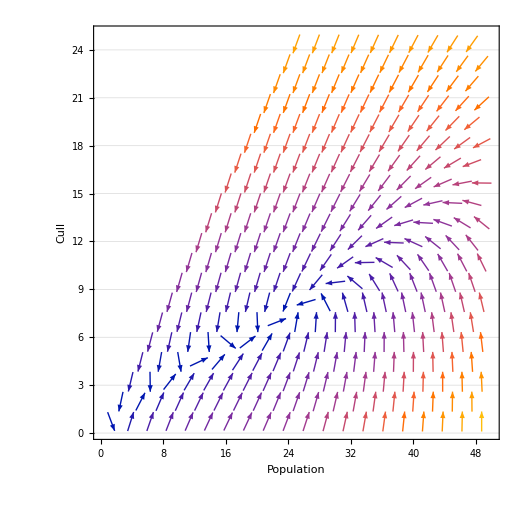

Part::partd: Part specification 50.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 25.⟦1⟧ is longer than depth of object.

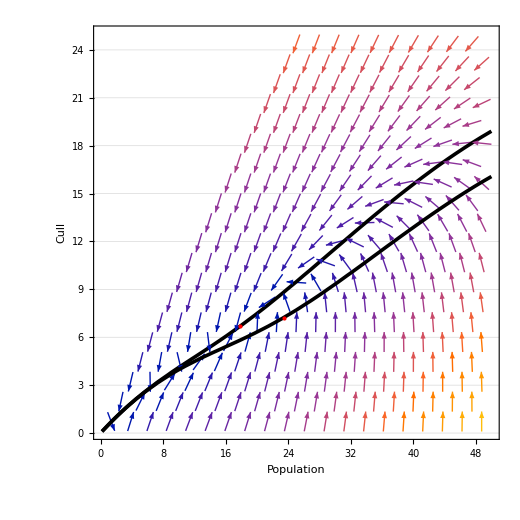

```mathematica
c1=130;
c0=100;
theta=50;
p=0.1;
r=0.584;
s=600;
delta=0.1;
d=0.25;
mu=0.1;
A=1;

Plot1a=VectorPlot[{f[Hs,Ns]-Ns,g[Hs,Ns]-Hs},{Ns,0.1,50},{Hs,0.1,25},(*Control of LINE OR POINT APPEARANCE*)VectorPoints->{20,20},VectorScale->{0.05,0.5},VectorStyle->{Gray},(*Restrict the vectors to the region where Ns>Hs*)RegionFunction->(#2<=#1&),RegionBoundaryStyle->None,RegionFillingStyle->None,(*#1 corresponds to Hs,and #2 to Ns*)(*Controls of Frame and AXES*)AxesOrigin->{-1,0},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->True,BaseStyle->{24,FontFamily->"Times"},GridLines->{None,Automatic},GridLinesStyle->Directive[Dashed],(*Controls of LABELS*)AspectRatio->1,ImageSize->520]

(*Plot only the rightmost contour line*)
Plot2a=ContourPlot[g[Hs,Ns]-Hs==0,{Ns,0.1,50},{Hs,0.1,25},ContourStyle->{Black,Thickness[0.005]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->False,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];

(*Extract the contour data*)
contours=Cases[Normal[Plot2a],Line[pts_]:>pts,Infinity];

(*Sort the contours by the maximum x-coordinate value*)
sortedContours=SortBy[contours,Max[#][[1]]&];

(*Extract the two rightmost contour lines*)
rightmostContour=sortedContours[[-1]];
(*Plot the two rightmost contour lines*)
Plot3a=Graphics[{Black,Thickness[0.005],Line[rightmostContour],Red,PointSize[Large],Point[{23.5,7.2}]},Frame->True,FrameLabel->{"Population","Harvest"},RotateLabel->True,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];
```

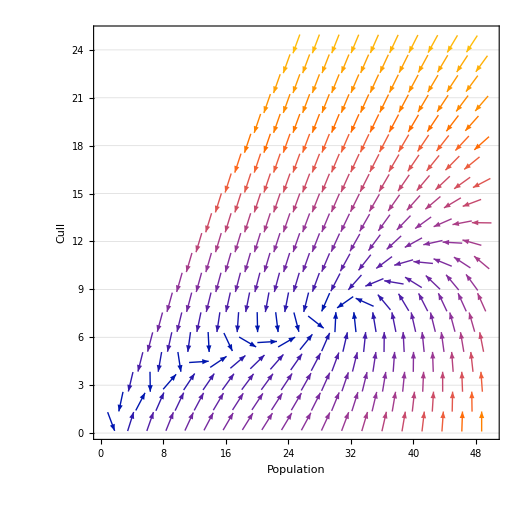

Part::partd: Part specification 50.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 25.⟦1⟧ is longer than depth of object.

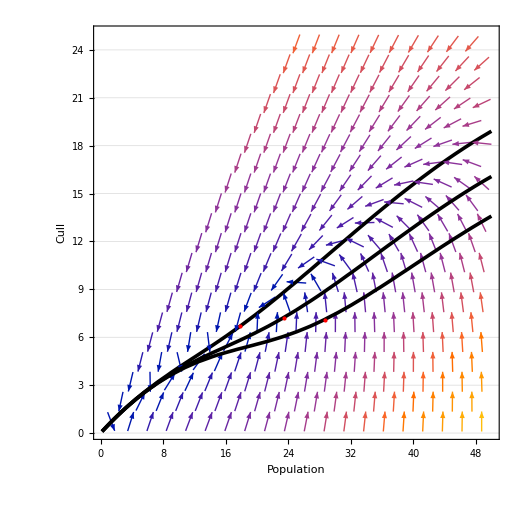

```mathematica
c1=130;
c0=100;
theta=50;
p=0.1;
r=0.584;
s=600;
delta=0.1;
d=0.15;
mu=0.1;
A=1;

Plot1b=VectorPlot[{f[Hs,Ns]-Ns,g[Hs,Ns]-Hs},{Ns,0.1,50},{Hs,0.1,25},(*Control of LINE OR POINT APPEARANCE*)VectorPoints->{20,20},VectorScale->{0.05,0.5},VectorStyle->{Gray},(*Restrict the vectors to the region where Ns>Hs*)RegionFunction->(#2<=#1&),RegionBoundaryStyle->None,RegionFillingStyle->None,(*#1 corresponds to Hs,and #2 to Ns*)(*Controls of Frame and AXES*)AxesOrigin->{-1,0},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->True,BaseStyle->{24,FontFamily->"Times"},GridLines->{None,Automatic},GridLinesStyle->Directive[Dashed],(*Controls of LABELS*)AspectRatio->1,ImageSize->520]

(*Plot only the rightmost contour line*)
Plot2b=ContourPlot[g[Hs,Ns]-Hs==0,{Ns,0.1,50},{Hs,0.1,25},ContourStyle->{Black,Thickness[0.005]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->False,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];

(*Extract the contour data*)
contours=Cases[Normal[Plot2b],Line[pts_]:>pts,Infinity];

(*Sort the contours by the maximum x-coordinate value*)
sortedContours=SortBy[contours,Max[#][[1]]&];

(*Extract the two rightmost contour lines*)
rightmostContour=sortedContours[[-1]];
(*Plot the two rightmost contour lines*)
Plot3b=Graphics[{Black,Thickness[0.005],Line[rightmostContour],Red,PointSize[Large],Point[{28.7,7.1}]},Frame->True,FrameLabel->{"Population","Harvest"},RotateLabel->True,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];
Show[Plot1,Plot3,Plot3a,Plot3b]
```

Part::partd: Part specification 50.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 25.⟦1⟧ is longer than depth of object.

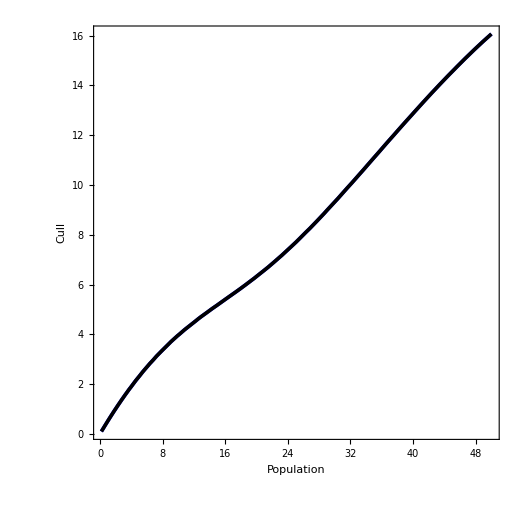

```mathematica
c1=130;
c0=100;
theta=50;
p=0.1;
r=0.584;
s=600;
delta=0.1;
d=0.25;
mu=0.1;
A=1;

Plot2=ContourPlot[g[Hs,Ns]-Hs==0,{Ns,0.1,50},{Hs,0.1,25},ContourStyle->{Blue,Thickness[0.005]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->False,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520, PlotLegends->Automatic];
(*Extract the contour data*)
contours=Cases[Normal[Plot2],Line[pts_]:>pts,Infinity];
(*Sort the contours by the maximum x-coordinate value*)
sortedContours=SortBy[contours,Max[#][[1]]&];
(*Extract the two rightmost contour lines*)
rightmostContour=sortedContours[[-1]];
(*Plot the two rightmost contour lines*)
Plot4=Graphics[{Blue,Thickness[0.005],Line[rightmostContour]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->True,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];
Show[Plot1,Plot4,Plot3]
```

Part::partd: Part specification 50.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 25.⟦1⟧ is longer than depth of object.

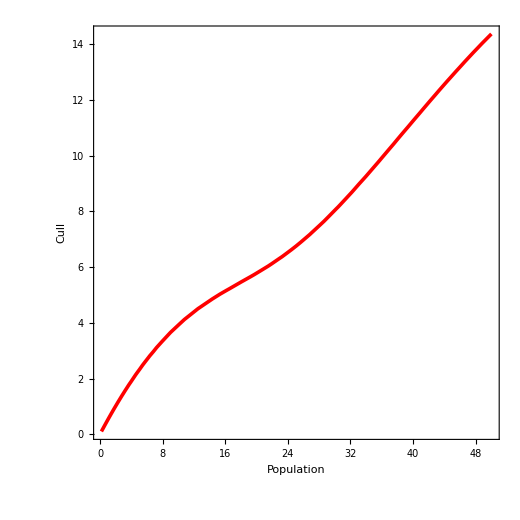

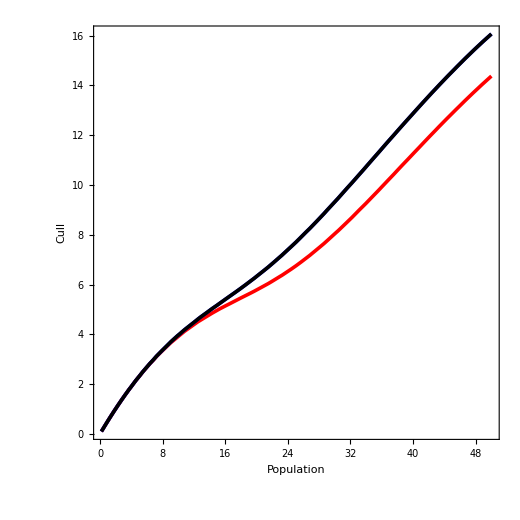

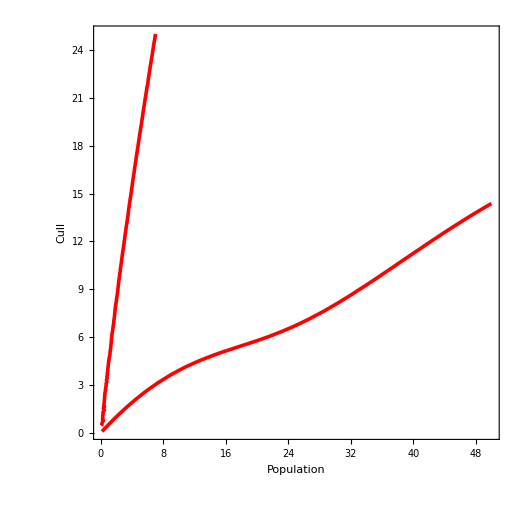

```mathematica
c1=130;
c0=100;
theta=50;
p=0.07;
r=0.584;
s=600;
delta=0.1;
d=0.25;
mu=0.1;
A=1;

Plot2=ContourPlot[g[Hs,Ns]-Hs==0,{Ns,0.1,50},{Hs,0.1,25},ContourStyle->{Red,Thickness[0.005]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->False,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520, PlotLegends->Automatic];
(*Extract the contour data*)
contours=Cases[Normal[Plot2],Line[pts_]:>pts,Infinity];
(*Sort the contours by the maximum x-coordinate value*)
sortedContours=SortBy[contours,Max[#][[1]]&];
(*Extract the two rightmost contour lines*)
rightmostContour=sortedContours[[-1]];
(*Plot the two rightmost contour lines*)
Plot5=Graphics[{Red,Thickness[0.005],Line[rightmostContour]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->True,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520,ShowLegends -> TRUE];
Show[Plot5]

Show[Plot5,Plot4,Plot3]

Plot2=ContourPlot[g[Hs,Ns]-Hs==0,{Ns,0.1,50},{Hs,0.1,25},ContourStyle->{Red,Thickness[0.005]},Frame->True,FrameLabel->{"Population","Cull"},RotateLabel->False,AspectRatio->1,AxesOrigin->{-1,0},Axes->False,BaseStyle->{24,FontFamily->"Times"},ImageSize->520];

(*Add a legend to the contour plot*)
PlotWithLegend=Legended[Plot2,"Contour of g[Hs, Ns] - Hs == 0"];

(*Show the plot with the legend*)
Show[PlotWithLegend]
```

```mathematica
Canvas[%713]
```

-Graphics-